# Embedded Pathways

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/embedded-pathways/analysis

## Data

### Ordination

```mathematica
ordinationData=Import["../results/ordination.tsv"];
```

```mathematica
headings=ordinationData[[1]]
```

{id,tsne_1,tsne_2,pca_1,pca_2,pca_3,pca_4,pca_5}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,headings]
```

{id→1,tsne_1→2,tsne_2→3,pca_1→4,pca_2→5,pca_3→6,pca_4→7,pca_5→8}

```mathematica
ordinationData=Drop[ordinationData,1];
```

```mathematica
nodes=Union[ordinationData[[All,1]]];
```

```mathematica
toTsne1=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,2}]]];
```

```mathematica
toTsne2=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,3}]]];
```

```mathematica
toPca1=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,4}]]];
```

```mathematica
toPca2=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,5}]]];
```

```mathematica
toPca3=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,6}]]];
```

```mathematica
toPca4=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,7}]]];
```

```mathematica
toPca5=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,8}]]];
```

### Metadata

```mathematica
metadata=Import["../data/metadata_embeddings.tsv"];
```

```mathematica
headings=metadata[[1]]
```

{name,parent,clade_membership,S1_mutations}

```mathematica
metadata=Drop[metadata,1];
```

```mathematica
toParent=Map[#[[1]]->#[[2]]&,metadata[[All,{1,2}]]];
```

```mathematica
toClade=Map[#[[1]]->If[StringQ[#[[2]]],StringSplit[#[[2]]," "][[1]],"other"]&,metadata[[All,{1,3}]]];
```

```mathematica
clades=Union[toClade[[All,2]]]
```

{19A,19B,20A,20B,20C,20D,20E,20G,20H,20I,20J,21A,21B,21C,21D,21F,21G,21H,21I,21J,21K,21L,21M,22A,22B,22C,22D,22E,22F,23A,23B,23C,23D,23E,23F,23G,23H,24A,24B,24C,24D,24E,24F,24G,24H,24I,25A,25B,25C,other}

### Embeddings

```mathematica
embeddingsData=Import["../results/embeddings.tsv"];
```

```mathematica
headings=embeddingsData[[1,1;;10]]
```

{NODE_0000000,-0.105426,-0.00601398,-0.0608945,-0.0861005,-0.040071,-0.0578419,0.0371932,-0.0463389,0.016354}

```mathematica
toEmbedding=Map[#[[1]]->#[[2;;-1]]&,embeddingsData];
```

## Clade colors

Download with “nextstrain remote download https://nextstrain.org/ncov/gisaid/global/all-time”

```mathematica
treeJson=Import["../data/auspice_embeddings.json","RawJSON"];
```

```mathematica
metaColorMapping=Map[StringSplit[#[[1]]," "][[1]]->RGBColor[#[[2]]]&,FirstCase[treeJson["meta"]["colorings"],x_/;x["key"]=="clade_membership"]["scale"]]
```

{20H→RGBColor[0.3686274509803922, 0.11372549019607843, 0.615686274509804],20I→RGBColor[0.30980392156862746, 0.12156862745098039, 0.6666666666666666],20J→RGBColor[0.28627450980392155, 0.1607843137254902, 0.7058823529411765],21A→RGBColor[0.2627450980392157, 0.2, 0.7450980392156863],21I→RGBColor[0.25098039215686274, 0.24705882352941178, 0.7764705882352941],21J→RGBColor[0.24705882352941178, 0.2980392156862745, 0.796078431372549],21B→RGBColor[0.24313725490196078, 0.34901960784313724, 0.8117647058823529],21C→RGBColor[0.25098039215686274, 0.4, 0.8117647058823529],21D→RGBColor[0.25882352941176473, 0.4470588235294118, 0.807843137254902],21F→RGBColor[0.26666666666666666, 0.49411764705882355, 0.8],21G→RGBColor[0.2823529411764706, 0.5294117647058824, 0.7764705882352941],21H→RGBColor[0.2980392156862745, 0.5686274509803921, 0.7529411764705882],21K→RGBColor[0.3176470588235294, 0.6, 0.7215686274509804],21L→RGBColor[0.33725490196078434, 0.6274509803921569, 0.6862745098039216],21M→RGBColor[0.3568627450980392, 0.6549019607843137, 0.6509803921568628],22A→RGBColor[0.3843137254901961, 0.6705882352941176, 0.611764705882353],22B→RGBColor[0.4117647058823529, 0.6901960784313725, 0.5686274509803921],22C→RGBColor[0.4392156862745098, 0.7058823529411765, 0.5294117647058824],22D→RGBColor[0.47058823529411764, 0.7137254901960784, 0.49411764705882355],22E→RGBColor[0.5019607843137255, 0.7254901960784313, 0.4549019607843137],22F→RGBColor[0.5372549019607843, 0.7333333333333333, 0.4196078431372549],23A→RGBColor[0.5725490196078431, 0.7372549019607844, 0.38823529411764707],23B→RGBColor[0.6078431372549019, 0.7450980392156863, 0.3568627450980392],23C→RGBColor[0.6431372549019608, 0.7450980392156863, 0.33725490196078434],23D→RGBColor[0.6823529411764706, 0.7411764705882353, 0.3137254901960784],23E→RGBColor[0.7176470588235294, 0.7411764705882353, 0.29411764705882354],23F→RGBColor[0.7529411764705882, 0.7333333333333333, 0.2784313725490196],23G→RGBColor[0.7843137254901961, 0.7215686274509804, 0.2627450980392157],23H→RGBColor[0.8156862745098039, 0.7058823529411765, 0.2549019607843137],24A→RGBColor[0.8392156862745098, 0.6862745098039216, 0.24313725490196078],24B→RGBColor[0.8666666666666667, 0.6666666666666666, 0.23529411764705882],24C→RGBColor[0.8784313725490196, 0.6352941176470588, 0.22745098039215686],24D→RGBColor[0.8941176470588236, 0.6, 0.2196078431372549],24E→RGBColor[0.9019607843137255, 0.5607843137254902, 0.21176470588235294],24F→RGBColor[0.9019607843137255, 0.5098039215686274, 0.20392156862745098],24G→RGBColor[0.9019607843137255, 0.4627450980392157, 0.19215686274509805],24H→RGBColor[0.8941176470588236, 0.403921568627451, 0.1803921568627451],24I→RGBColor[0.8862745098039215, 0.3411764705882353, 0.16862745098039217],25A→RGBColor[0.8745098039215686, 0.2784313725490196, 0.1568627450980392],25B→RGBColor[0.8666666666666667, 0.2196078431372549, 0.14901960784313725],25C→RGBColor[0.8588235294117647, 0.1568627450980392, 0.13725490196078433]}

Non-variant clades need to be assigned grays

```mathematica
earlyColorMapping=MapThread[#1->#2&,{{"19A","19B","20A","20B","20C","20D","20E","20F","20G","21F","other"},Table[GrayLevel[x],{x,0.25,0.75,0.5/10}]}]
```

{19A→GrayLevel[0.25],19B→GrayLevel[0.3],20A→GrayLevel[0.35],20B→GrayLevel[0.4],20C→GrayLevel[0.45],20D→GrayLevel[0.5],20E→GrayLevel[0.55],20F→GrayLevel[0.6000000000000001],20G→GrayLevel[0.65],21F→GrayLevel[0.7],other→GrayLevel[0.75]}

```mathematica
cladeToColor=Join[earlyColorMapping,metaColorMapping]
```

{19A→GrayLevel[0.25],19B→GrayLevel[0.3],20A→GrayLevel[0.35],20B→GrayLevel[0.4],20C→GrayLevel[0.45],20D→GrayLevel[0.5],20E→GrayLevel[0.55],20F→GrayLevel[0.6000000000000001],20G→GrayLevel[0.65],21F→GrayLevel[0.7],other→GrayLevel[0.75],20H→RGBColor[0.3686274509803922, 0.11372549019607843, 0.615686274509804],20I→RGBColor[0.30980392156862746, 0.12156862745098039, 0.6666666666666666],20J→RGBColor[0.28627450980392155, 0.1607843137254902, 0.7058823529411765],21A→RGBColor[0.2627450980392157, 0.2, 0.7450980392156863],21I→RGBColor[0.25098039215686274, 0.24705882352941178, 0.7764705882352941],21J→RGBColor[0.24705882352941178, 0.2980392156862745, 0.796078431372549],21B→RGBColor[0.24313725490196078, 0.34901960784313724, 0.8117647058823529],21C→RGBColor[0.25098039215686274, 0.4, 0.8117647058823529],21D→RGBColor[0.25882352941176473, 0.4470588235294118, 0.807843137254902],21F→RGBColor[0.26666666666666666, 0.49411764705882355, 0.8],21G→RGBColor[0.2823529411764706, 0.5294117647058824, 0.7764705882352941],21H→RGBColor[0.2980392156862745, 0.5686274509803921, 0.7529411764705882],21K→RGBColor[0.3176470588235294, 0.6, 0.7215686274509804],21L→RGBColor[0.33725490196078434, 0.6274509803921569, 0.6862745098039216],21M→RGBColor[0.3568627450980392, 0.6549019607843137, 0.6509803921568628],22A→RGBColor[0.3843137254901961, 0.6705882352941176, 0.611764705882353],22B→RGBColor[0.4117647058823529, 0.6901960784313725, 0.5686274509803921],22C→RGBColor[0.4392156862745098, 0.7058823529411765, 0.5294117647058824],22D→RGBColor[0.47058823529411764, 0.7137254901960784, 0.49411764705882355],22E→RGBColor[0.5019607843137255, 0.7254901960784313, 0.4549019607843137],22F→RGBColor[0.5372549019607843, 0.7333333333333333, 0.4196078431372549],23A→RGBColor[0.5725490196078431, 0.7372549019607844, 0.38823529411764707],23B→RGBColor[0.6078431372549019, 0.7450980392156863, 0.3568627450980392],23C→RGBColor[0.6431372549019608, 0.7450980392156863, 0.33725490196078434],23D→RGBColor[0.6823529411764706, 0.7411764705882353, 0.3137254901960784],23E→RGBColor[0.7176470588235294, 0.7411764705882353, 0.29411764705882354],23F→RGBColor[0.7529411764705882, 0.7333333333333333, 0.2784313725490196],23G→RGBColor[0.7843137254901961, 0.7215686274509804, 0.2627450980392157],23H→RGBColor[0.8156862745098039, 0.7058823529411765, 0.2549019607843137],24A→RGBColor[0.8392156862745098, 0.6862745098039216, 0.24313725490196078],24B→RGBColor[0.8666666666666667, 0.6666666666666666, 0.23529411764705882],24C→RGBColor[0.8784313725490196, 0.6352941176470588, 0.22745098039215686],24D→RGBColor[0.8941176470588236, 0.6, 0.2196078431372549],24E→RGBColor[0.9019607843137255, 0.5607843137254902, 0.21176470588235294],24F→RGBColor[0.9019607843137255, 0.5098039215686274, 0.20392156862745098],24G→RGBColor[0.9019607843137255, 0.4627450980392157, 0.19215686274509805],24H→RGBColor[0.8941176470588236, 0.403921568627451, 0.1803921568627451],24I→RGBColor[0.8862745098039215, 0.3411764705882353, 0.16862745098039217],25A→RGBColor[0.8745098039215686, 0.2784313725490196, 0.1568627450980392],25B→RGBColor[0.8666666666666667, 0.2196078431372549, 0.14901960784313725],25C→RGBColor[0.8588235294117647, 0.1568627450980392, 0.13725490196078433]}

```mathematica
variantLegend=SwatchLegend[Table[clade/.cladeToColor,{clade,clades}],Table[clade,{clade,clades}],LegendLayout->{"Row",1}];
```

```mathematica
smallVariantLegend=SwatchLegend[Table[clade/.cladeToColor,{clade,clades}],Table[clade,{clade,clades}],LegendLayout->{"Column",1},LabelStyle->{FontSize->10}];
```

## Ordinations

```mathematica
figFromOrdinationRules[dimen1_,dimen2_,xLabel_,yLabel_]:=Module[{points,lines,colors,pointFig,lineFig},
points=Table[Tooltip[{node/.dimen1,node/.dimen2},node],{node,nodes}];
lines=Table[With[{parent=node/.toParent},{{node/.dimen1,node/.dimen2},{parent/.dimen1,parent/.dimen2}}],{node,nodes}];
colors=Table[node/.toClade/.cladeToColor,{node,nodes}];
pointFig=ListPlot[Map[{#}&,points],PlotTheme->"FulLAxes",PlotRange->All,ImageSize->400,Frame->{True,True,False,False},FrameLabel->{xLabel,yLabel},Axes->False,PlotStyle->colors,PlotMarkers->{"•",Small}];
lineFig=ListLinePlot[lines,PlotTheme->"FulLAxes",PlotRange->All,ImageSize->400,Frame->{True,True,False,False},FrameLabel->{xLabel,yLabel},Axes->False,PlotStyle->Directive[AbsoluteThickness[1],Opacity[0.25],GrayLevel[0.25]]];
Show[lineFig,pointFig]
]
```

```mathematica
pca12Fig=figFromOrdinationRules[toPca1,toPca2,"PCA dimen 1", "PCA dimen 2"];
```

```mathematica
pca13Fig=figFromOrdinationRules[toPca1,toPca3,"PCA dimen 1", "PCA dimen 3"];
```

```mathematica
pca14Fig=figFromOrdinationRules[toPca1,toPca4,"PCA dimen 1", "PCA dimen 4"];
```

```mathematica
pca23Fig=figFromOrdinationRules[toPca2,toPca3,"PCA dimen 2", "PCA dimen 3"];
```

```mathematica
pca24Fig=figFromOrdinationRules[toPca2,toPca4,"PCA dimen 2", "PCA dimen 4"];
```

```mathematica
pca34Fig=figFromOrdinationRules[toPca3,toPca4,"PCA dimen 3", "PCA dimen 4"];
```

```mathematica
fig=Grid[{{pca12Fig,"",""},{pca13Fig,pca23Fig,""},{pca14Fig,pca24Fig,pca34Fig}}];
```

```mathematica
fig=Export["figures/pca_grid.png",fig,"PNG",ImageResolution->300]
```

figures/pca_grid.png

## Direct embeddings

```mathematica
embeddingStandardDeviations=Map[StandardDeviation,Transpose[Table[node/.toEmbedding,{node,nodes}]]];
```

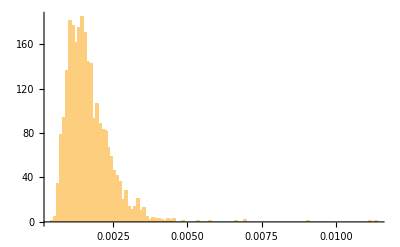

```mathematica
Histogram[embeddingStandardDeviations,100,PlotRange->All]
```

```mathematica
pos=Position[embeddingStandardDeviations,x_/;x>0.02]
```

{}

```mathematica
Reverse[Ordering[embeddingStandardDeviations]][[1;;5]]
```

{2503,1513,697,462,1930}

```mathematica
extractEmbedding[dimen_]:=Map[#[[1]]->#[[2,dimen]]&,toEmbedding]
```

```mathematica
figFromOrdinationRules[extractEmbedding[1161],extractEmbedding[235],"Embedding"];
```

```mathematica
figFromOrdinationRules[extractEmbedding[877],extractEmbedding[691],"Embedding"];
```